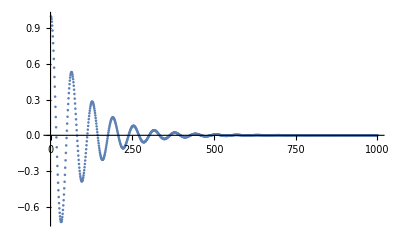

```mathematica
(*(∂_t)^2 x=-0.2∂_t x-x*)
L=N@({{0, 1}, {-1, -0.2}});
δt=0.1;
tN=1000;
A= Inverse[IdentityMatrix[2]-δt/2 L.(IdentityMatrix[2]-δt/6 L)].(δt*L);
fsol=Table[0,{i,1,tN}];
fsol[[1]]={1,0};
For[ii=1,ii<=tN-1,ii++,fsol[[ii+1]]=fsol[[ii]]+A.fsol[[ii]]]
ListPlot[fsol[[All,1]],PlotRange->All]
```

```mathematica
NSolve[(-I*ω)^2+0.2(-I*ω)+1==0]
```

{{ω→-0.994987-0.1 ⅈ},{ω→0.994987-0.1 ⅈ}}

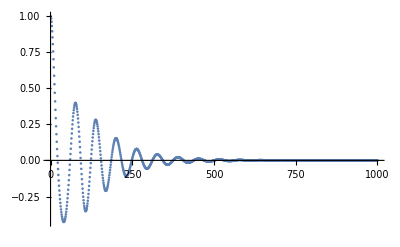

```mathematica
(*(∂_t)^2 x=-0.2∂_t x-x+0.5Sin[t]*)
evolve[x_,v_,t_]:={v,-x-0.2v+0.5Exp[-0.25t]Sin[1.2t],1}
x=1;v=0;t=0;st=0.1;times=1000;result={};
Monitor[Label["ev"];Ry1=evolve[x,v,t];(*1<->2*)
Ry2=evolve@@({x,v,t}+st/2 Ry1);(*2<->3*)
Ry3=evolve@@({x,v,t}+st/2 Ry2);(*3<->4*)
Ry4=evolve@@({x,v,t}+st*Ry3);
{x,v,t}+=st/6(Ry1+2Ry2+2Ry3+Ry4);times=times-1;result=Append[result,{x,v,t}];If[times>0,Goto["ev"]],times]
ListPlot[data=result[[All,1]],PlotRange->All]
```

1000

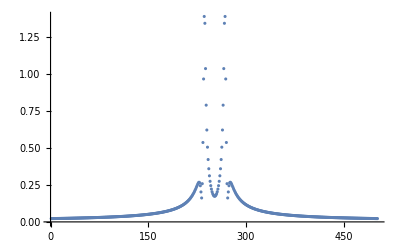

```mathematica
n=Length[data]
f=Fourier[data];
ListPlot[Abs[f[[n/2+1;;n]]~Join~f[[1;;n/2]]][[250;;-250]],PlotRange->All]
```

```mathematica
p=4;m=800;s=0;
det[k_]:=Det[{Table[z^i,{i,0,p}]}~Join~Table[data[[(j+k);;(j+k+p)]],{j,1,p}]]
sol=NSolve[Sum[det[k],{k,s,s+m-1}],z]
10I*Log[z]/.sol
```

{{z→0.968347-0.117514 ⅈ},{z→0.968347+0.117514 ⅈ},{z→0.985109-0.0973347 ⅈ},{z→0.985109+0.0973347 ⅈ}}

{1.20765-0.248547 ⅈ,-1.20765-0.248547 ⅈ,0.984864-0.101456 ⅈ,-0.984864-0.101456 ⅈ}

```mathematica
(*Matrix pencil方法*)
p=4;
X=Table[data[[(j);;(j+p-1)]],{j,1,n-p}];
Y=Table[data[[(j+1);;(j+p)]],{j,1,n-p}];
10I*Log@Eigenvalues[PseudoInverse[X].Y]
```

{-0.994987-0.0999996 ⅈ,0.994987-0.0999996 ⅈ,-1.2-0.25 ⅈ,1.2-0.25 ⅈ}

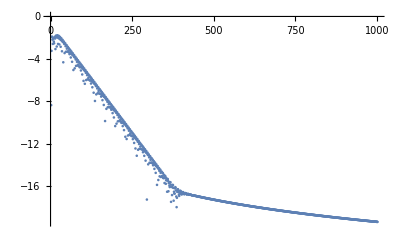

{0.809963-0.0942554 ⅈ,-0.809963-0.0942554 ⅈ,0.-0.190862 ⅈ,1.31509-0.191338 ⅈ,-1.31509-0.191338 ⅈ,0.797156-0.284499 ⅈ,-0.797156-0.284499 ⅈ,0.-0.902866 ⅈ}

```mathematica
data$raw=Import["/Volumes/KIOXIA-SD10/Projects/Tails/Julia_version/[3030][40]/psi4_I.csv"];
data$raw=data$raw[[2;;-1,1]];
ListPlot[Log10[Abs[data$raw]],PlotRange->All]
data=data$raw[[50;;-1]];
n=Length[data];
p=8;
X=Table[data[[(j);;(j+p-1)]],{j,1,n-p}];
Y=Table[data[[(j+1);;(j+p)]],{j,1,n-p}];
Sort[I*Log@Eigenvalues[PseudoInverse[X].Y],Im[#1]>Im[#2]&]
```

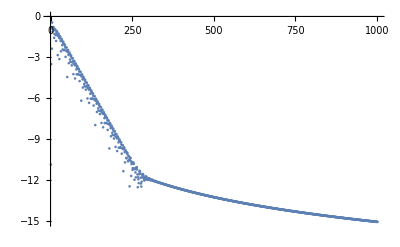

{0.657536-0.09572 ⅈ,-0.657536-0.09572 ⅈ,0.-0.164376 ⅈ,0.643009-0.29032 ⅈ,-0.643009-0.29032 ⅈ,0.599001-0.465452 ⅈ,-0.599001-0.465452 ⅈ,0.-0.629129 ⅈ}

```mathematica
data$raw=Import["/Volumes/KIOXIA-SD10/Projects/Tails/Julia_version/[3030][40]/phi2_I.csv"];
data$raw=data$raw[[2;;-1,1]];
ListPlot[Log10[Abs[data$raw]],PlotRange->All]
data=data$raw[[28;;-1]];
n=Length[data];
p=8;
X=Table[data[[(j);;(j+p-1)]],{j,1,n-p}];
Y=Table[data[[(j+1);;(j+p)]],{j,1,n-p}];
Sort[I*Log@Eigenvalues[PseudoInverse[X].Y],Im[#1]>Im[#2]&]
```